# Parametric Daisy Pendant by Marin Azhar

The design of the Parametric Daisy Chain represents the simplistic beauty of symmetry and the complexity of mathematics in nature.

## Inspiration:

```mathematica
Manipulate[PolarPlot[r= Cos[a*t],{t,0,2*Pi}],{a,0,10,1}]
```

## Using the Polar plot function and the Manipulate function i was able to see experent on the diffent types of shapes the Cos[t] function can make.

## Turning into a 3D flower using ParametricPlot3D:

```mathematica
f2= ParametricPlot3D[{Cos[4*t]Cos[t] +1, Cos[4*t]Sin[t] +1, u}, {t,0,2Pi}, {u,0, 0.25},Extrusion -> 0.1,Mesh-> 100,PlotRange->All]

zero = ParametricPlot3D[{ 0.71 -0.45Cos[t]Cos[t] ,1.52 -0.45Cos[t]Sin[t] , u }, {t,0,2Pi}, {u,0, 0.25},Mesh-> 100,Extrusion -> 0.1,PlotRange->All]
```

-Graphics3D-

-Graphics3D-

From here I was able to create the desired objects needed for the construction of my pendant. I gave it the depth of 0.25 to make it as thin as possible while still keeping it 3D. I added a mesh of 100 so the curves will be smooth however it does make Mathematica load shower. The Plot Range --> All was used so that when i showed the objects none of them would be cropped out. In the show function all of the objects are placed on the same axis/location thus i added +1 for every object so that they would be shown next to each other and not on top of each other.

## Creating interlocking hoops:

```mathematica
Manipulate[Show[ParametricPlot3D[{ 0.71 -0.45Cos[t]Cos[t] ,1.52 -0.45Cos[t]Sin[t] , u }, {t,0,2Pi}, {u,0, 0.15},Extrusion -> 0.1,PlotRange->All]
,  ParametricPlot3D[{ n -0.45Cos[t]Sin[t] ,r+u, m-0.45Cos[t]Cos[t] }, {t,0,2Pi}, {u,0, 0.15},Extrusion -> 0.1,PlotRange->All]], {n,-3,3},{m,-3,3},{r,-3,3}]
```

```mathematica
DynamicModule[{m=0.33999999999999986,n=0.31000000000000005,r=1.4100000000000001},Show[ParametricPlot3D[{0.71-0.45 Cos[t] Cos[t],1.52-0.45 Cos[t] Sin[t],u},{t,0,2 π},{u,0,0.15},Extrusion->0.1,PlotRange->All],ParametricPlot3D[{n-0.45 Cos[t] Sin[t],r+u,m-0.45 Cos[t] Cos[t]},{t,0,2 π},{u,0,0.15},Extrusion->0.1,PlotRange->All]]]
```

```mathematica
twohoops =Show[ParametricPlot3D[{0.71-0.45 Cos[t] Cos[t],1.52-0.45 Cos[t] Sin[t],u},{t,0,2 π},{u,0,0.15},Extrusion->0.1,PlotRange->All],ParametricPlot3D[{00.31000000000000005-0.45 Cos[t] Sin[t],1.41+u,0.33999999999999986-0.45 Cos[t] Cos[t]},{t,0,2 π},{u,0,0.15},Extrusion->0.1,PlotRange->All]]
```

-Graphics3D-

Getting a screenshot from the dynamic model of the interlocking hoops and then showing it to call it one function. The first hoops coordinates are set to the candidates on top of the second flower; thus, only the second hoops location had to be manipulated in order to get the desired results for the next step when showing both the pendant and the hoops.

## Final Result:

```mathematica
project22=Show[twohoops,f2]
f7= ParametricPlot3D[{Cos[4*t]Cos[t] -2, Cos[4*t]Sin[t]+2,  u}, {t,0,2Pi}, {u,0, 0.25},Extrusion -> 0.1,Mesh-> 100,PlotRange->All]
Export["project2.2necklace.stl",project22]
Manipulate[Show[project22, ParametricPlot3D[{a+Cos[4*t]Cos[t] ,b + Cos[4*t]Sin[t],  u}, {t,0,2Pi}, {u,0, 0.25},Extrusion -> 0.1,Mesh-> 100,PlotRange->All]],{a,-3,3},{b,-3,3}]
```

-Graphics3D-

-Graphics3D-

project2.2necklace.stl

Show::gcomb: Could not combine the graphics objects in ….

The final result is a Daisy chain with a interlocking hoop

## Helpful Scratch Work:

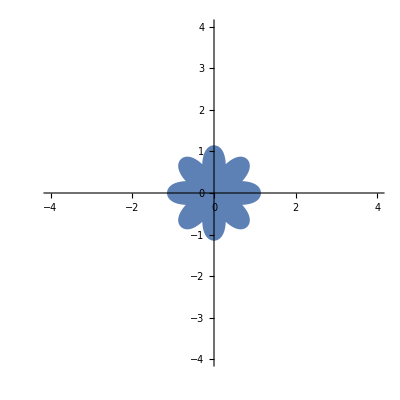

DiscretePlot::pllim: Range specification {1} is not of the form {x, xmin, xmax}.

DiscretePlot[flower,{1}]

MeshCoordinates[-Graphics-]

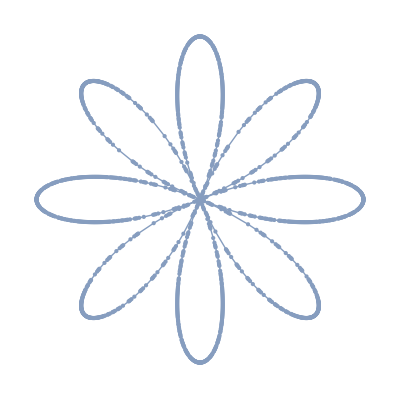

```mathematica
flower=Graphics[ PolarPlot[ Table [r= (Cos[4*t ])],{t,0,2*Pi} , PlotRange->4 ,PlotStyle->{Thickness[0.022]}  ]
]
DiscretePlot[flower, {1}]
MeshCoordinates[flower]
disFlower =DiscretizeGraphics[flower]
```

I learned that using the DiscretizeGraphics function over a Polar function does not give the give the graphics any volume.